```mathematica
Clear[Lx,Ly,A,
sx3d,SX3D,sx3dp,SX3DP,
sy3d,SY3D,sy3dp,SY3DP,
sz3d,SZ3D,sz3dp,SZ3DP,
cx3d,CX3D,cx3dp,CX3DP,
cy3d,CY3D,cy3dp,CY3DP,
cz3d,CZ3D,cz3dp,CZ3DP,
cons,Cons]
```

```mathematica
Lx=8;
Ly=8;
Lz =4;
A=Lx*Ly*Lz;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sx3d[j+k Lx+l Lx Ly,j+1+k Lx + l Lx Ly]=-I/2,sx3d[j+1+k Lx + l Lx Ly,j+k Lx+l Lx Ly]=I/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

SX3D=Table[sx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx3dp[i_Integer,j_Integer]=0;

Do[Do[{sx3dp[(k+1)Lx+ l Lx Ly,1+k Lx+ l Lx Ly]=-I/2,sx3dp[1+k Lx+ l Lx Ly,(k+1)Lx+ l Lx Ly]=I/2},{k,0,Ly-1}],{l,0,Lz-1}]

SX3DP=Table[sx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=-I/2,sy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

SY3D=Table[sy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy3dp[i_Integer,j_Integer]=0;

Do[Do[{sy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=-I/2,sy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{l,0,Lz-1}]

SY3DP=Table[sy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cx3d[j+k Lx+l Lx Ly,j+1+k Lx+l Lx Ly]=1/2,cx3d[j+1+k Lx+l Lx Ly,j+k Lx+l Lx Ly]=1/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

CX3D=Table[cx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx3dp[i_Integer,j_Integer]=0;

Do[Do[{cx3dp[(1+k)Lx+l Lx Ly,1+k Lx+l Lx Ly]=1/2,cx3dp[1+k Lx+l Lx Ly,(1+k)Lx+l Lx Ly]=1/2},{k,0,Ly-1}],{l,0,Lz-1}]

CX3DP=Table[cx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=1/2,cy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

CY3D=Table[cy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy3dp[i_Integer,j_Integer]=0;

Do[Do[{cy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=1/2,cy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{l,0,Lz-1}]

CY3DP=Table[cy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cz3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cz3d[j+(k-1) Lx+(l-1) Lx Ly,j+(k-1)Lx+l Lx Ly]=1/2,cz3d[j+(k-1)Lx+l Lx Ly,j+(k-1) Lx+(l-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}],{l,1,Lz-1}]

CZ3D=Table[cz3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cz3dp[i_Integer,j_Integer]=0;

Do[Do[{cz3dp[(k-1)Lx+j+(Lz-1) Lx Ly,(k-1)Lx+j]=1/2,cz3dp[(k-1)Lx+j,(k-1)Lx+j+(Lz-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}]

CZ3DP=Table[cz3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0;

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM[t_,t0_,m_,tz_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]+KroneckerProduct[(tz *(CZ2D + α*CZ2DP)-m)*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM[1.,1.,4,1,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

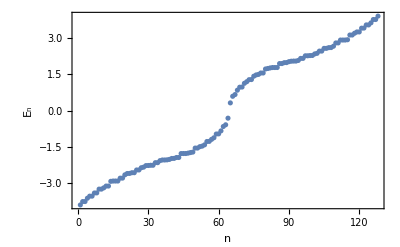

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],(**Plot[0,{x,0,2A},PlotStyle-> Red],**)BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
val[[Lx*Ly*Lz/2]]
```

Part::partw: Part 512 of {-3.90418,3.90418,-3.7644,3.7644,-3.76356,3.76356,-3.62686,3.62686,3.54049,-3.54049,«118»} does not exist.

{-3.90418,3.90418,-3.7644,3.7644,-3.76356,3.76356,-3.62686,3.62686,3.54049,-3.54049,3.54043,-3.54043,-3.41033,3.41033,-3.40593,3.40593,-3.24989,3.24989,3.24928,-3.24928,-3.19718,3.19718,-3.12345,3.12345,3.1228,-3.1228,-2.92757,2.92757,2.91541,-2.91541,2.91537,-2.91537,-2.91526,2.91526,-2.79673,2.79673,2.79431,-2.79431,-2.65977,2.65977,-2.60473,2.60473,-2.60075,2.60075,2.57173,-2.57173,-2.57133,2.57133,2.45869,-2.45869,-2.45793,2.45793,-2.36529,2.36529,-2.34101,2.34101,-2.27719,2.27719,-2.27311,2.27311,2.26362,-2.26362,-2.26353,2.26353,-2.15668,2.15668,-2.15575,2.15575,-2.07155,2.07155,2.04548,-2.04548,2.04541,-2.04541,2.03973,-2.03973,2.02121,-2.02121,-1.98248,1.98248,-1.97947,1.97947,1.94255,-1.94255,1.94223,-1.94223,1.7791,-1.7791,1.77809,-1.77809,1.77775,-1.77775,-1.76136,1.76136,1.73826,-1.73826,-1.71812,1.71812,-1.5524,1.5524,1.55171,-1.55171,1.49361,-1.49361,1.47144,-1.47144,1.41902,-1.41902,-1.28086,1.28086,1.27533,-1.27533,-1.19184,1.19184,-1.12592,1.12592,0.971815,-0.971815,0.964788,-0.964788,-0.841654,0.841654,-0.660506,0.660506,-0.589187,0.589187,-0.316022,0.316022}⟦512⟧

```mathematica
vec[[512]]
```

Part::partw: Part 512 of {{-0.0153846-0.0153846 ⅈ,0.00421307+5.89535×10^-19 ⅈ,-0.0311408-0.030931 ⅈ,0.00605626+0.00257445 ⅈ,-0.0428308-0.0426416 ⅈ,0.00709931+0.00481014 ⅈ,-0.0490219-0.0489494 ⅈ,0.00722761+0.00642999 ⅈ,-0.0489494-0.0490219 ⅈ,0.00642999+0.00722761 ⅈ,«118»},«9»,«118»} does not exist.

{{-0.0153846-0.0153846 ⅈ,0.00421307+5.89535×10^-19 ⅈ,-0.0311408-0.030931 ⅈ,0.00605626+0.00257445 ⅈ,-0.0428308-0.0426416 ⅈ,0.00709931+0.00481014 ⅈ,-0.0490219-0.0489494 ⅈ,0.00722761+0.00642999 ⅈ,-0.0489494-0.0490219 ⅈ,0.00642999+0.00722761 ⅈ,109,-0.00642999-0.00722761 ⅈ,-0.0490219-0.0489494 ⅈ,-0.00722761-0.00642999 ⅈ,-0.0428308-0.0426416 ⅈ,-0.00709931-0.00481014 ⅈ,-0.0311408-0.030931 ⅈ,-0.00605626-0.00257445 ⅈ,-0.0153846-0.0153846 ⅈ,-0.00421307+0. ⅈ},126,{1}}⟦512⟧
 |  |  |  |

```mathematica
b=ValVecAHI[[512]][[2]];
```

Part::partw: Part 512 of {{-3.90418,{-0.0153846-0.0153846 ⅈ,0.00421307+5.89535×10^-19 ⅈ,-0.0311408-0.030931 ⅈ,0.00605626+0.00257445 ⅈ,-0.0428308-0.0426416 ⅈ,0.00709931+0.00481014 ⅈ,-0.0490219-0.0489494 ⅈ,0.00722761+0.00642999 ⅈ,-0.0489494-0.0490219 ⅈ,0.00642999+0.00722761 ⅈ,«118»}},«9»,«118»} does not exist.

```mathematica
a=Abs[b]*Abs[b];
```

```mathematica
DensityVector = {};Do[Do[Do[DensityVector=Append[DensityVector,{i,j,k,a[[i + (j-1)*Lx + (k-1)*Lx * Ly]]+a[[i + (j-1)*Lx + (k-1)*Lx * Ly+Lx*Ly*Lz]]}],{i,1,Lx}],{j,1,Ly}],{k,1,Lz}]
```

Part::partd: Part specification 262144⟦1⟧ is longer than depth of object.

Part::partd: Part specification 262144⟦65⟧ is longer than depth of object.

Part::partd: Part specification 262144⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Quit[]
```

```mathematica
DensityVector;
```

```mathematica
Export["densityvector.dat",DensityVector];
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,50]
```

{-3.14159,-3.01593,-2.89027,-2.7646,-2.63894,-2.51327,-2.38761,-2.26195,-2.13628,-2.01062,-1.88496,-1.75929,-1.63363,-1.50796,-1.3823,-1.25664,-1.13097,-1.00531,-0.879646,-0.753982,-0.628319,-0.502655,-0.376991,-0.251327,-0.125664,0.,0.125664,0.251327,0.376991,0.502655,0.628319,0.753982,0.879646,1.00531,1.13097,1.25664,1.3823,1.50796,1.63363,1.75929,1.88496,2.01062,2.13628,2.26195,2.38761,2.51327,2.63894,2.7646,2.89027,3.01593,3.14159}

```mathematica
aaaaa=Dimensions[kzVector][[1]]
```

51

```mathematica
(**OBC**)
```

```mathematica
(* Clear[b];
b={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM[1.,1.,4,1,kzVector[[i]],0]],
Do[b=Append[b,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,aaaaa}] *)
```

```mathematica
(* ListPlot[b] *)
```

```mathematica
(**PBC**)
```

```mathematica
(*Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM[1.,1.,4,1,kzVector[[i]],1]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,aaaaa}]*)
```

```mathematica
(*ListPlot[bb]*)
```

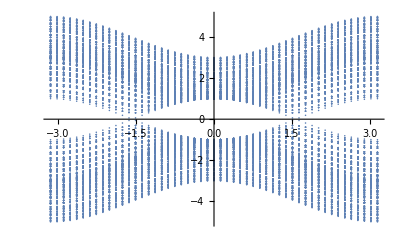

-Graphics-

```mathematica
(**----Clear memory for quasicrystal----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

2048

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+5
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+3
```

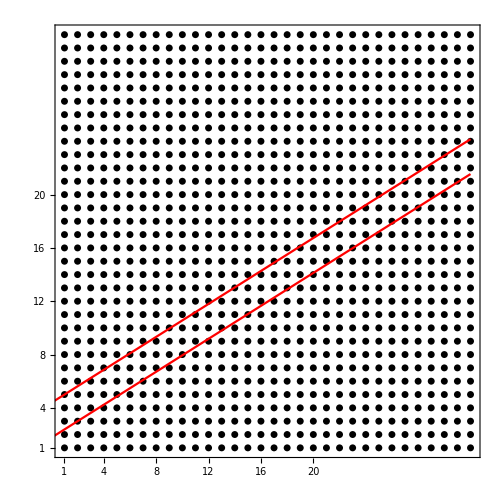

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy, P,U,V,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{65,97,98,99,130,131,132,133,163,164,165,166,197,198,199,200,230,231,232,233,234,264,265,266,267,298,299,300,301,331,332,333,334,365,366,367,368,398,399,400,401,402,432,433,434,435,466,467,468,469,499,500,501,502,503,533,534,535,536,567,568,569,570,600,601,602,603,634,635,636,637,667,668,669,670,671,701,702,703,704,735,736,768}

```mathematica
NSitesQuasi2D = Dimensions[FibonList][[1]];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
FibonList3D = {};
```

```mathematica
Do[Do[FibonList3D = Append[FibonList3D,FibonList[[k]]+z*Lx*Ly],{k,1,NSitesQuasi2D}],{z,0,Lz-1}]
```

```mathematica
Clear[FibonList];
```

```mathematica
FibonList = FibonList3D;
```

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{129,130,193,194,195,196,197,198,259,260,261,262,263,264,265,266,325,326,327,328,329,330,331,332,393,394,395,396,397,398,399,400,459,460,461,462,463,464,465,466,467,468,527,528,529,530,531,532,533,534,595,596,597,598,599,600,601,602,661,662,663,664,665,666,667,668,729,730,731,732,733,734,735,736,795,796,797,798,799,800,801,802,803,804,863,864,865,866,867,868,869,870,931,932,933,934,935,936,937,938,997,998,999,1000,1001,1002,1003,1004,1005,1006,1065,1066,1067,1068,1069,1070,1071,1072,1133,1134,1135,1136,1137,1138,1139,1140,1199,1200,1201,1202,1203,1204,1205,1206,1267,1268,1269,1270,1271,1272,1273,1274,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1401,1402,1403,1404,1405,1406,1407,1408,1469,1470,1471,1472,1535,1536}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

166

```mathematica
NOrbitalsQuasi/2
```

83

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

1882

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.0810547

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{2048}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(**-------------------------------**)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2-1}]
```

{{1.,0},{1.85065,0},{2.37638,0},{3.22703,0},{3.75276,0},{4.60341,0},{5.45407,0},{5.9798,0},{6.83045,0},{7.6811,0},{8.20683,0},{9.05748,0},{9.58321,0},{10.4339,0},{11.2845,0},{11.8102,0},{12.6609,0},{13.5115,0},{14.0373,0},{14.8879,0},{15.4137,0},{16.2643,0},{17.115,0},{17.6407,0},{18.4913,0},{19.0171,0},{19.8677,0},{20.7184,0},{21.2441,0},{22.0948,0},{22.9454,0},{23.4711,0},{24.3218,0},{24.8475,0},{25.6982,0},{26.5488,0},{27.0746,0},{27.9252,0},{28.4509,0},{29.3016,0},{30.1522,0},{30.678,0},{31.5286,0},{32.3793,0},{32.905,0},{33.7557,0},{34.2814,0},{35.132,0},{35.9827,0},{36.5084,0},{37.3591,0},{38.2097,0},{38.7354,0},{39.5861,0},{40.1118,0},{40.9625,0},{41.8131,0},{42.3389,0},{43.1895,0},{43.7152,0},{44.5659,0},{45.4165,0},{45.9423,0},{46.7929,0},{47.6436,0},{48.1693,0},{49.02,0},{49.5457,0},{50.3963,0},{51.247,0},{51.7727,0},{52.6234,0},{53.1491,0},{53.9998,0},{54.8504,0},{55.3761,0},{56.2268,0},{57.0774,0},{57.6032,0},{58.4538,0},{58.9796,0},{59.8302,0},{60.6809,0}}

```mathematica
Clear[xx,yy]
```

```mathematica
xx={};
yy={};
```

```mathematica
Do[{s=Solve[y==LineDn[x]&& (y-YList[[k]])/(x-XList[[k]])==-((1+√5)/2) ,{x,y}],xx = Append[xx,s[[All,1,2]]],yy = Append[yy,s[[All,2,2]]]},{k,1,NOrbitalsQuasi/2}]
```

```mathematica
N[xx]
```

{{1.27639},{1.72361},{2.44721},{3.17082},{2.89443},{3.61803},{4.34164},{5.06525},{4.06525},{4.78885},{5.51246},{6.23607},{5.95967},{6.68328},{7.40689},{8.1305},{7.1305},{7.8541},{8.57771},{9.30132},{10.0249},{9.02492},{9.74853},{10.4721},{11.1957},{10.9193},{11.643},{12.3666},{13.0902},{12.0902},{12.8138},{13.5374},{14.261},{13.9846},{14.7082},{15.4318},{16.1554},{15.1554},{15.879},{16.6026},{17.3262},{18.0498},{17.0498},{17.7735},{18.4971},{19.2207},{18.9443},{19.6679},{20.3915},{21.1151},{20.1151},{20.8387},{21.5623},{22.2859},{23.0095},{22.0095},{22.7331},{23.4567},{24.1803},{23.9039},{24.6276},{25.3512},{26.0748},{25.0748},{25.7984},{26.522},{27.2456},{26.9692},{27.6928},{28.4164},{29.14},{28.14},{28.8636},{29.5872},{30.3108},{31.0344},{30.0344},{30.758},{31.4817},{32.2053},{31.9289},{32.6525},{33.0997}}

```mathematica
N[yy]
```

{{2.55279},{2.82918},{3.27639},{3.72361},{3.55279},{4.},{4.44721},{4.89443},{4.27639},{4.72361},{5.17082},{5.61803},{5.44721},{5.89443},{6.34164},{6.78885},{6.17082},{6.61803},{7.06525},{7.51246},{7.95967},{7.34164},{7.78885},{8.23607},{8.68328},{8.51246},{8.95967},{9.40689},{9.8541},{9.23607},{9.68328},{10.1305},{10.5777},{10.4069},{10.8541},{11.3013},{11.7485},{11.1305},{11.5777},{12.0249},{12.4721},{12.9193},{12.3013},{12.7485},{13.1957},{13.643},{13.4721},{13.9193},{14.3666},{14.8138},{14.1957},{14.643},{15.0902},{15.5374},{15.9846},{15.3666},{15.8138},{16.261},{16.7082},{16.5374},{16.9846},{17.4318},{17.879},{17.261},{17.7082},{18.1554},{18.6026},{18.4318},{18.879},{19.3262},{19.7735},{19.1554},{19.6026},{20.0498},{20.4971},{20.9443},{20.3262},{20.7735},{21.2207},{21.6679},{21.4971},{21.9443},{22.2207}}

```mathematica
N[Sqrt[xx^2+yy^2]]
```

{{2.8541},{3.31287},{4.08945},{4.89074},{4.58258},{5.39353},{6.21511},{7.04359},{5.90032},{6.72648},{7.55808},{8.3935},{8.07402},{8.91126},{9.75082},{10.5921},{9.4299},{10.2706},{11.1128},{11.9562},{12.8006},{11.634},{12.478},{13.3229},{14.1684},{13.8454},{14.6913},{15.5377},{16.3846},{15.2144},{16.0611},{16.9082},{17.7557},{17.4319},{18.2796},{19.1275},{19.9756},{18.8036},{19.6516},{20.4999},{21.3484},{22.197},{21.0243},{21.8728},{22.7215},{23.5704},{23.2462},{24.0951},{24.9442},{25.7933},{24.6198},{25.469},{26.3182},{27.1675},{28.0169},{26.8431},{27.6924},{28.5419},{29.3914},{29.0669},{29.9164},{30.766},{31.6157},{30.4415},{31.2912},{32.1409},{32.9906},{32.666},{33.5158},{34.3656},{35.2155},{34.041},{34.8909},{35.7407},{36.5907},{37.4406},{36.266},{37.116},{37.9659},{38.8159},{38.4912},{39.3413},{39.8666}}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

61

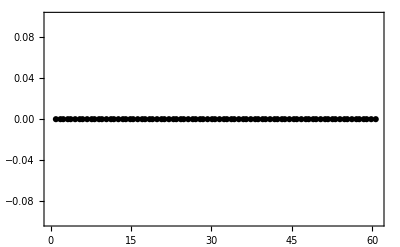

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(**-------------------------------**)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[TabFibNew, TabRenorEnergies]
```

```mathematica
TabFibNew={}
```

{}

```mathematica
TabRenorEnergies={}
```

{}

```mathematica
Do[{Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial=HamiltonianWSM[1.,1.,4,1,kzVector[[p]],0],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
(**------Check that HFibonRenor is Hermitian------**)
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor],
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First],
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop,
(*Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-100,100},PlotStyle-> Red]]*)
(** without dislocation -1 OBC **)
(** without dislocation +1 OBC **)
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}],
Tr[OnlyEigenvalue]//Chop,
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)],
NSitesInside = NOrbitalsQuasi/2,
(*---------------------------------------------------------------------------------------------------------*)
(*---------------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------------------------------------*)
ValFibon[[(NOrbitalsQuasi/2)+1,2]],
Clear[J,TabDataFibon,TDFibon],
J=NOrbitalsQuasi/2;,
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2

},{i,1,NOrbitalsQuasi/2}],
TDFibon=Flatten[TabDataFibon],
Do[TabFibNew = Append[TabFibNew,{TDFibon[[i]],kzVector[[p]],TDFibon[[i+2]]}],{i,1,3*NOrbitalsQuasi/2,3}],
Do[TabRenorEnergies = Append[TabRenorEnergies,{kzVector[[p]],OnlyEigenvalue[[i]]}],{i,1,NOrbitalsQuasi}]
},{p,1,aaaaa}]
```

$Aborted

```mathematica
(* TabFibNew=Import["/home/archisman/Documents/GitHub/quasicrystals/results/WSM/OBC/one-set-data/WSM-high-occ-density.dat"]; *)
```

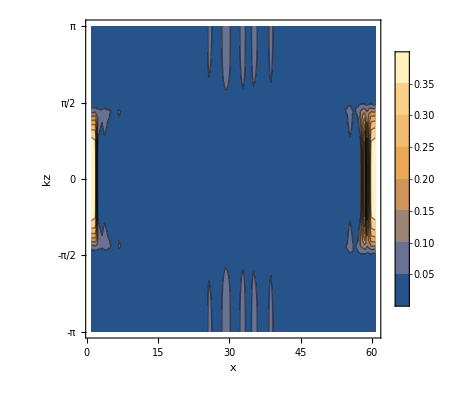

```mathematica
P33=ListContourPlot[TabFibNew,PlotRange->All, FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,FrameLabel-> {"x","kz"},FrameTicks->{{{-π,-π/2,0,π/2,π},None},{Automatic,None}},PlotLegends->Automatic]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
(** colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]]; **)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0+1*v/vmax,1,1-0.3 v/vmax,v/vmax]];
```

```mathematica
Hue[0,0.5,0.5]
```

Hue[0, 0.5, 0.5]

```mathematica
Hue[0.69,0.5,0.5]
```

Hue[0.69, 0.5, 0.5]

```mathematica
colorfunc[0.2,2]
```

Hue[0.1, 1, 0.97, 0.1]

```mathematica
rng={0,Max[#]}&@TabFibNew[[All,3]];
```

```mathematica
rng[[2]]
```

0.398546

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.076"},{rng[[2]]-10^-3,"0.152"}}]
```

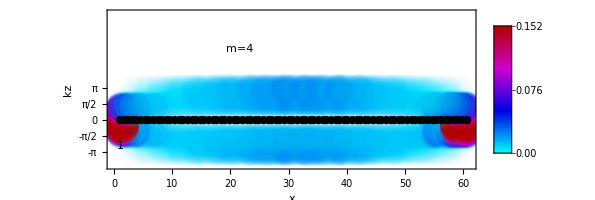

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNew,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX},{-4.5,10.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
FrameTicks->{{{-π,-π/2,0,π/2,π},None},{Automatic,None}},FrameLabel-> {"x","kz"},
Epilog-> {Inset[1,{1,-2.5}],
Rotate[Inset[P1,{11,7.00}],90 Degree],Inset["m=4",{21.5,7}]
(* ,Inset["(a)",{1.25,7}]*)
}
]
```

```mathematica
TabFibNewNewFromPiby2Only = {};
```

```mathematica
Do[If[Abs[TabFibNew[[ii]][[2]]]<π/2,TabFibNewNewFromPiby2Only=Append[TabFibNewNewFromPiby2Only,TabFibNew[[ii]]]],{ii,1,Dimensions[TabFibNew][[1]]}]
```

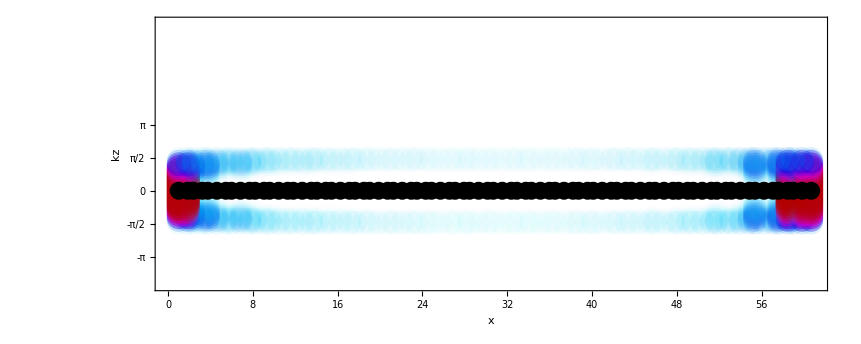

```mathematica
Show[Graphics[{PointSize[0.02],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNewNewFromPiby2Only,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX},{-4.5,8}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
FrameTicks->{{{-π,-π/2,0,π/2,π},None},{Automatic,None}},FrameLabel-> {"x","kz"}
]
```

```mathematica
TabFibNewNewFromPiby2Only[[1;;2]]
```

{{1.,-1.50796,0.0223864},{1.85065,-1.50796,0.0280489}}

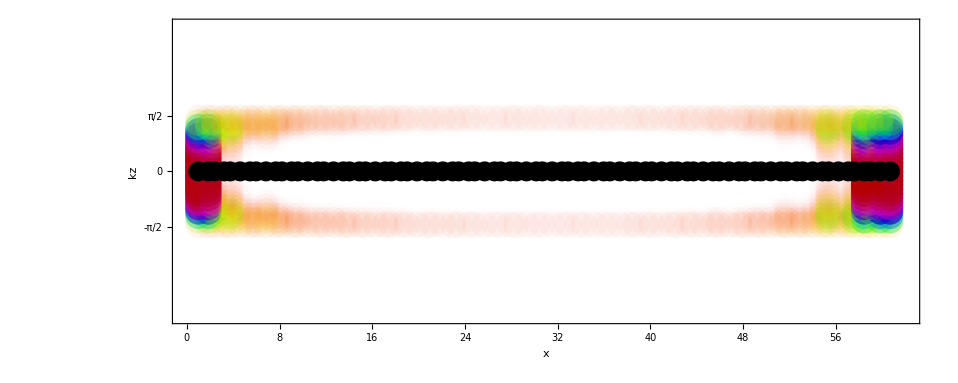

```mathematica
Show[Graphics[{PointSize[0.02],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNewNewFromPiby2Only,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX+1},{-π-1,π+1}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
FrameTicks->{{{-π/2,0,π/2},None},{Automatic,None}},FrameLabel-> {"x","kz"}
]
```

```mathematica
Export["WSMTabfibnewdata_m4_up+5_dn+3.dat",TabFibNewNewFromPiby2Only];
```

```mathematica
Export["Fibon1D.dat",Fibon1D];
```

```mathematica
TabFibNew2=Import["WSMTabfibnewdata_m4_up+4_dn+2.dat"];
```

```mathematica
(* Export["/home/archisman/Documents/GitHub/quasicrystals/results/WSM/PBC/one-set-data/WSM-high-occ-density.dat",TabFibNew]; *)
```

```mathematica
(***---- Calculation of energy eigenvalues for different kz---***)
```

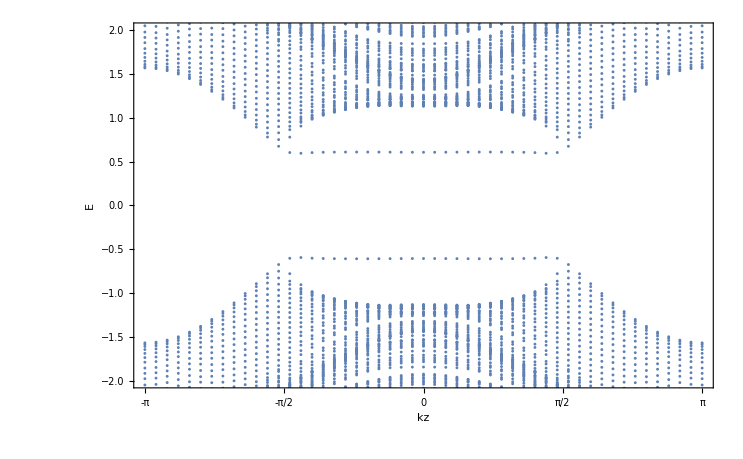

```mathematica
ListPlot[TabRenorEnergies,Frame->True,FrameStyle-> Black,
BaseStyle-> 18,FrameLabel->{"kz","E"},FrameTicks->{Automatic,{{-π,-π/2,0,π/2,π},None}},PlotRange->{Automatic,{-2,2}}]
```

```mathematica
(** Small y axis width **)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

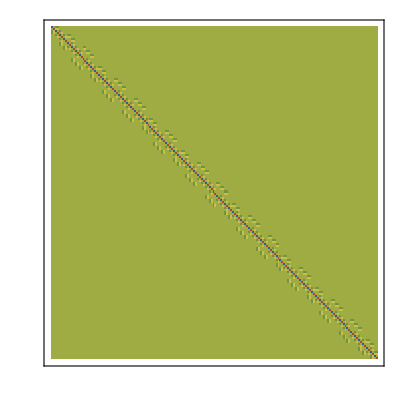

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

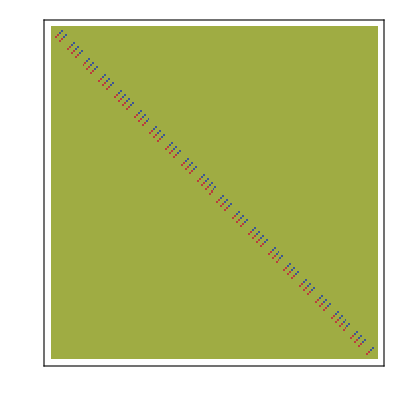

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

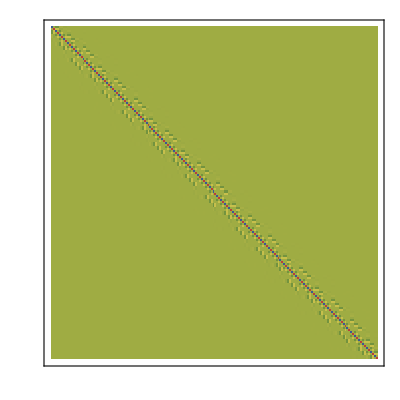

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

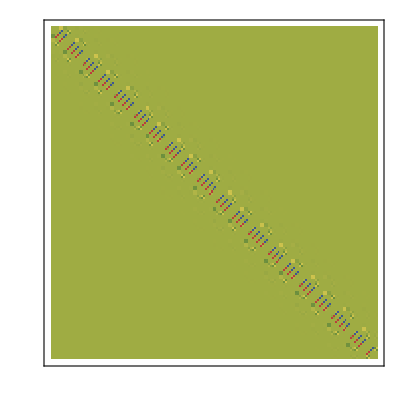

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```